```mathematica
eq1=C1*s*Vc[s]-C1*v0[t]-Vo[s]*Ra/(R2*(Ra+Rb))==0;
```

```mathematica
eq2=Vc[s]-Vo[s]+C1*(R1+R2)*(s*Vc[s]-v0[t])+L1*C1*(s^2*Vc[s]-s*v0[t])==0;
```

```mathematica
sol1=Solve[{eq1,eq2},{Vo[s],v0[t]}]
```

{{Vo[s]→(R2 (Ra+Rb) Vc[s])/(-R1 Ra+R2 Rb-L1 Ra s),v0[t]→-(-Ra Vc[s]-C1 R1 Ra s Vc[s]+C1 R2 Rb s Vc[s]-C1 L1 Ra s^2 Vc[s])/(C1 (R1 Ra-R2 Rb+L1 Ra s))}}

```mathematica
H[s]=Cancel[Extract[sol1,{1,1,2}]/Extract[sol1,{1,2,2}]]
```

(C1 R2 (Ra+Rb))/(-Ra-C1 R1 Ra s+C1 R2 Rb s-C1 L1 Ra s^2)

Si se cumple que R1=R2*Rb/Ra entonces ξ=0

```mathematica
Ho[s]=Cancel[H[s]/. {R1-> (R2*Rb)/Ra}]
```

-(C1 R2 (Ra+Rb))/(Ra (1+C1 L1 s^2))

```mathematica
polos=TransferFunctionPoles[TransferFunctionModel[Ho[s],s]]
```

{{{-ⅈ/(√C1 √L1),ⅈ/(√C1 √L1)}}}

```mathematica
InverseLaplaceTransform[Ho[s],s,t]/.Ra->Rb
```

-(2 √C1 R2 Sin[t/(√C1 √L1)])/(√L1)

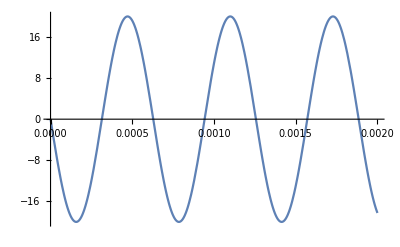

```mathematica
Plot[%/.{C1->1*10^-6,L1->10*10^-3,R2->1000},{t,0,0.002}]
```

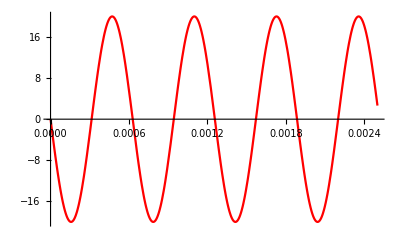

```mathematica
graf1t=Plot[InverseLaplaceTransform[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->1000,R1->1000},s,t],{t,0,0.0025},PlotRange->All,PlotStyle->Red]
```

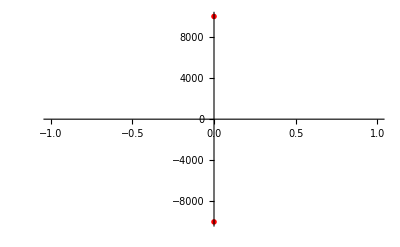

```mathematica
graf1p=ListPlot[({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->1000,R1->1000},s]],{1,1}])),PlotMarkers->{"X",20},PlotStyle->Red,PlotRange->All]
```

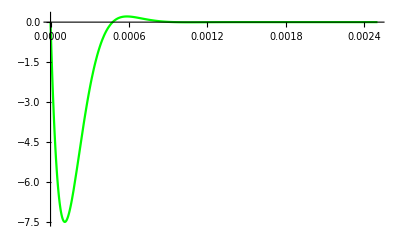

```mathematica
graf2t=Plot[InverseLaplaceTransform[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->850,R1->1000},s,t],{t,0,0.0025},PlotRange->All,PlotStyle->Green]
```

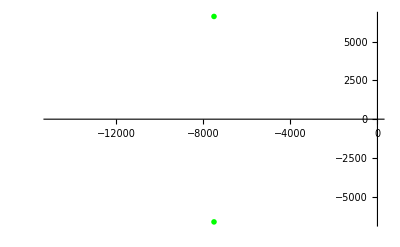

```mathematica
graf2p=ListPlot[({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->850,R1->1000},s]],{1,1}])),PlotMarkers->{"X",20},PlotStyle->Green,PlotRange->All]
```

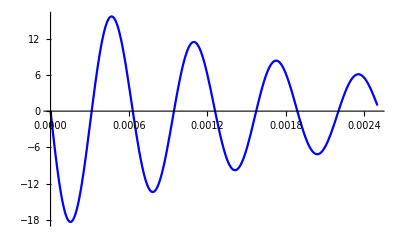

```mathematica
graf3t=Plot[InverseLaplaceTransform[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->990,R1->1000},s,t],{t,0,0.0025},PlotRange->All,PlotStyle->Blue]
```

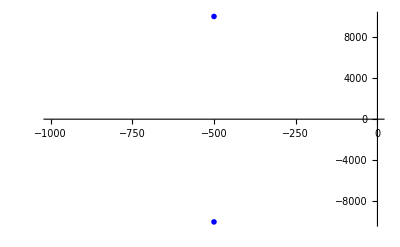

```mathematica
graf3p=ListPlot[({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->990,R1->1000},s]],{1,1}])),PlotMarkers->{"X",20},PlotStyle->Blue,PlotRange->All]
```

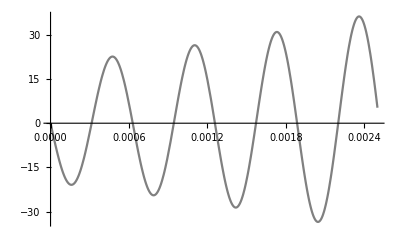

```mathematica
graf4t=Plot[InverseLaplaceTransform[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->1005,R1->1000},s,t],{t,0,0.0025},PlotRange->All,PlotStyle->Gray]
```

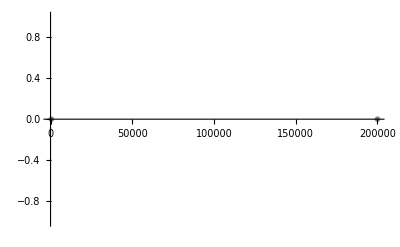

```mathematica
graf4p=ListPlot[({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->3005,R1->1000},s]],{1,1}])),PlotMarkers->{"X",20},PlotStyle->Gray,PlotRange->All]
```

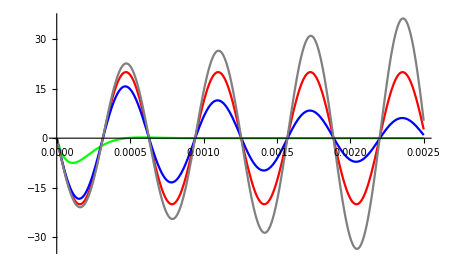

```mathematica
Show[graf1t,graf2t,graf3t,graf4t]
```

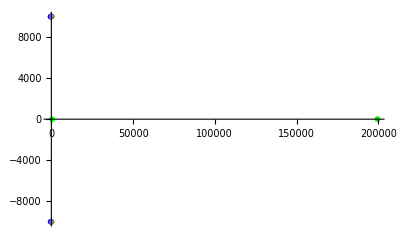

```mathematica
ListPlot[{({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->1000,R1->1000},s]],{1,1}])),({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->3000,R1->1000},s]],{1,1}])),({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->990,R1->1000},s]],{1,1}])),({Re@#,Im@#}&/@(Extract[TransferFunctionPoles[TransferFunctionModel[H[s]/.{Ra->Rb,C1->1*10^-6,L1->10*10^-3,R2->1005,R1->1000},s]],{1,1}]))},PlotMarkers->{"X",20},PlotStyle->{Red,Green,Blue,Gray},PlotRange->All]
```

```mathematica
H2[s]=TransferFunctionModel[H[s]/.{Ra->1000,Rb->1000,C1->1*10^-6,L1->10*10^-3,R1->1000},s]
```

R2/(500 (-1000-s+(R2 s)/1000-s^2/100000))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111-10001FalseFalseFalseAutomaticNoneAutomatic

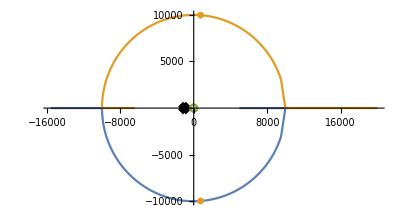

```mathematica
RootLocusPlot[H2[s],{R2,780,1250}]
```